```mathematica
αcont=SetPrecision[{0.5137193759431391,0.0024666827878353577},100]; 
σcont=SetPrecision[{0.16955497884544793,0.0008581023195660334},100];
```

### Complex permittivity in real space

```mathematica
Limit[Assuming[{a∈Reals,a>0,mD∈Reals,mD>0,r∈Reals,r>0},Integrate[p^4/(p^2+mD^2)Exp[-a p]Sinc[p r],{p,0,∞}]],a->0]//FullSimplify
```

(mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]))/(2 r)

```mathematica
N[Log[-ⅈ x]-Log[ⅈ x]/.x->10]
```

0.-3.14159 ⅈ

```mathematica
(mD^2 π(Sinh[mD r]-Cosh[mD r] ))/(2 r)//FullSimplify
```

-(ⅇ^(-mD r) mD^2 π)/(2 r)

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0},Integrate[(p^3 mD^2)/((p^2+mD^2)^2)Sinc[p r],{p,0,∞}]]//FullSimplify
```

(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r)

```mathematica
(4π)/(2π)^3(-(ⅇ^(-mD r) mD^2 π)/(2 r)-ⅈ π T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r))
```

(-(ⅇ^(-mD r) mD^2 π)/(2 r)-(ⅈ mD π^(3/2) T MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r))/(2 π^2)

```mathematica
ϵ[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

```mathematica
ϵp[p_,mD_,T_]:=p^2/(p^2+mD^2)-ⅈ π T(p mD^2)/((p^2+mD^2)^2);
```

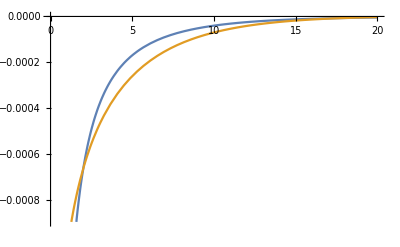

```mathematica
Plot[{Re[ϵ[x,15/100,155/1000]],Im[ϵ[x,15/100,155/1000]]},{x,0,20}]
```

## Checking Debye - Huckel solutions

### Coulomb Real

```mathematica
ReVc[r_,mD_,α_]:=-α Exp[-mD r]/r-α mD;
```

```mathematica
D[-α Exp[-mD r]/r,{r,2}]+2/r D[-α Exp[-mD r]/r,r]//FullSimplify
```

-(ⅇ^(-mD r) mD^2 α)/r

```mathematica
ReVclhs[r_,mD_,α_,T_]:=-(ⅇ^(-mD r) mD^2 α)/r;(*analytically correct*)
```

### Coulomb Imag

```mathematica
ImVc[r_,mD_,α_,T_]:=α T Quiet[NIntegrate[2 z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]];
```

```mathematica
-Laplacian[-Sinc[mD r z],{r,θ,ϕ},"Spherical"]//FullSimplify
```

-(mD z Sin[mD r z])/r

```mathematica
ImVclhs[r_,mD_,α_,T_]:=-α T NIntegrate[2 z/((z^2+1)^2)(mD z Sin[mD r z])/r,{z,0,∞},MaxRecursion->20,WorkingPrecision->100];
```

```mathematica
N[ImVclhs[10,15/100,αcont[[1]],155/1000],100]
```

-0.000449292642896475517792672448124988349953350622536405713660299369400309524486128256784074466934007732

```mathematica
N[4π αcont[[1]]Im[ϵ[10,15/100,155/1000]],100]
```

-0.0004492926428964755177926724481249883499533506225364057476349410209992435376005007923033479865840584338

```mathematica
(*for string part*)
```

```mathematica
Integrate[Integrate[-4 π σ (-mD z r Sin[mD r z]),r],r]//FullSimplify
```

-(4 π σ (2 Cos[mD r z]+mD r z Sin[mD r z]))/(mD^2 z^2)

### String Real

```mathematica
ReVs0[r_,mD_,α_,σ_]:=-Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4)) ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

```mathematica
-1/r^2 D[ReVs0[r,mD,α,σ],{r,2}]//FullSimplify
```

(σ Gamma[5/4] (2 α ((mD^2 σ)/α)^(3/4) Hypergeometric0F1Regularized[3/4,(mD^2 r^4 σ)/(16 α)]-mD^2 r σ Hypergeometric0F1Regularized[5/4,(mD^2 r^4 σ)/(16 α)]))/α

```mathematica
ReVs0lhs[r_,mD_,α_,σ_]:=(σ Gamma[5/4] (2 α ((mD^2 σ)/α)^(3/4) Hypergeometric0F1Regularized[3/4,(mD^2 r^4 σ)/(16 α)]-mD^2 r σ Hypergeometric0F1Regularized[5/4,(mD^2 r^4 σ)/(16 α)]))/α;
```

```mathematica
ReVs0lhs[10,15/100,αcont[[1]],σcont[[1]]]
```

0.000033766811055921791248733796404566997186977247318262193208645864153104000313750663469652947384733

```mathematica
4π αcont[[1]]Re[ϵ[5,15/100,0]]
```

-0.001091987328107366900376931498131946412754219922995321935405446277986579584422683668701088848777567799

### String Imag

## Attempt to solve for String part

### Real

```mathematica
Integrate[-4 π σ r^2 ϵ[r,mD,T],r]
```

mD σ (-(ⅇ^(-mD r) (1+mD r))/mD+1/2 ⅈ √π r^2 T MeijerG[{{-1/2},{}},{{1/2,1/2},{-1}},(mD^2 r^2)/4])

```mathematica
ReVs1[r_,mD_,σ_]:=-σ Exp[-mD r](1+mD r)
```

```mathematica
Integrate[ReVs1[r,mD,σ],r]//FullSimplify
```

(ⅇ^(-mD r) (2+mD r) σ)/mD

```mathematica
ReVs[r_,mD_,σ_]:=(ⅇ^(-mD r) σ (2+mD r))/mD;
```

```mathematica
Series[ReVs[r,mD,σ],{mD,0,3}]//FullSimplify
```

(2 σ)/mD-r σ+1/6 r^3 σ mD^2-1/12 (r^4 σ) mD^3+O[mD]^4

```mathematica
ReVs[r_,mD_,σ_]:=(2σ)/mD-(ⅇ^(-mD r) σ (2+mD r))/mD;(*introduces an overall extra minus sign from ODE solution*)
```

```mathematica
Series[ReVs[r,mD,σ],{mD,0,1}]//FullSimplify
```

r σ+O[mD]^2

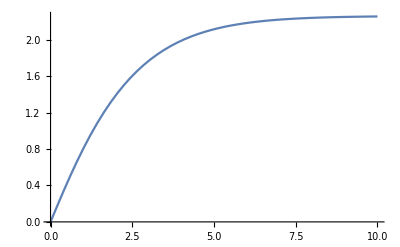

```mathematica
Plot[ReVs[r 1000/197,15/100,σcont[[1]]],{r,0,10}]
```

```mathematica
ReVsold[r_,mD_,α_,σ_]:=-Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]+Gamma[1/4]/(2 Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

```mathematica
(*check nummerically that solution holds*)
```

```mathematica
checktab=ParallelTable[{r,ReVs[r,15/100,σcont[[1]]]},{r,10^-10,350,1/100}];
```

```mathematica
checkinter=Interpolation[checktab];
```

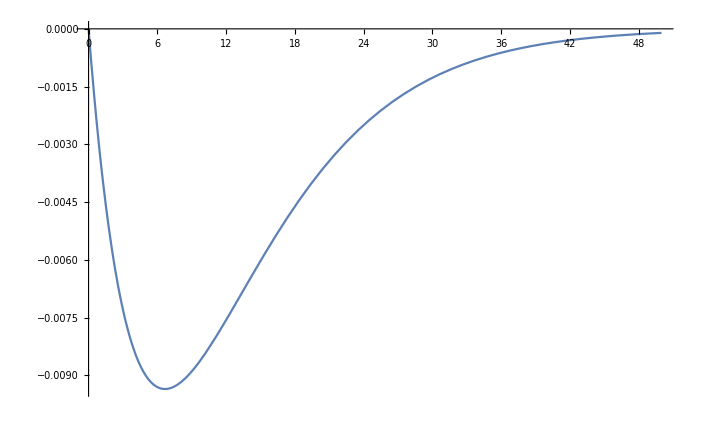

```mathematica
Plot[checkinter''[x],{x,0,50},PlotRange->All]
```

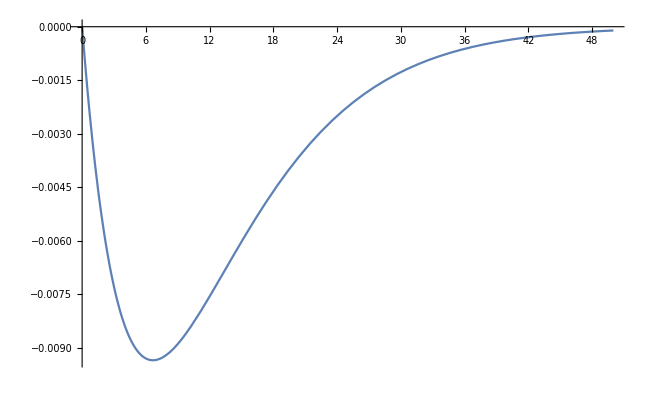

```mathematica
Plot[4π σcont[[1]] r^2 Re[ϵ[r,15/100,0]],{r,0,50},PlotRange->All]
```

### Imaginary

```mathematica
4 π σ r^2 ϵ[r,mD,T]//Simplify
```

-ⅇ^(-mD r) mD r σ (mD+ⅈ ⅇ^(mD r) √π T MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])

```mathematica
Integrate[-4 π σ r^2 ϵ[r,mD,T],r]
```

mD σ (-(ⅇ^(-mD r) (1+mD r))/mD+1/2 ⅈ √π r^2 T MeijerG[{{-1/2},{}},{{1/2,1/2},{-1}},(mD^2 r^2)/4])

```mathematica
ImVs1[r_,mD_,σ_,T_]:=(√π mD σ T)/2 r^2 MeijerG[{{-1/2},{}},{{1/2,1/2},{-1}},(mD^2 r^2)/4];
```

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0},Series[ImVs1[r,mD,σ,T],{r,0,3}]]//FullSimplify
```

-1/9 (mD^2 T σ (-5+6 EulerGamma+3 Log[mD^2]+6 Log[r])) r^3+O[r]^4

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0},Series[ImVs1[r,mD,σ,T],{r,∞,3}]]//FullSimplify
```

((4 T σ)/(mD^2 r)+O[1/r]^2)+ⅇ^(-mD r) (-1/2 ⅈ mD π T σ r^2-1/2 ⅈ π T σ r-(ⅈ π T σ)/(2 mD)+O[1/r]^2)

```mathematica
Integrate[ImVs1[r,mD,σ,T],r]
```

1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4]

```mathematica
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

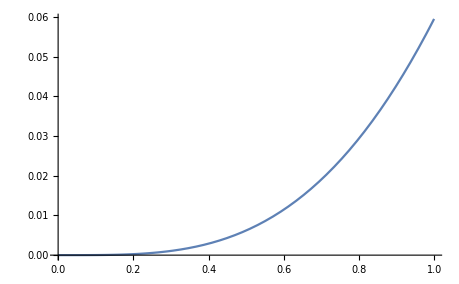

```mathematica
Plot[ImVs[r 1000/197,15/100,σcont[[1]],155/1000],{r,0,1}]
```

```mathematica
ImVs[100 1000/197,15/100,σcont[[1]],155/1000]
```

18.2641460779320986798115488258935764304046326805130079816091071851995474080958963608193351853784459

```mathematica
(*check nummerically that solution holds*)
```

```mathematica
checktab=ParallelTable[{r,ImVs[r,15/100,σcont[[1]],155/1000]},{r,10^-10,50,1/100}];
```

```mathematica
checkinter=Interpolation[checktab];
```

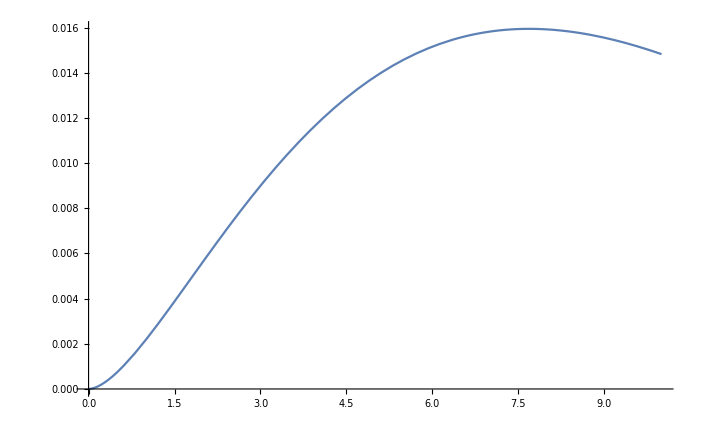

```mathematica
Plot[checkinter''[x],{x,0,10},PlotRange->All]
```

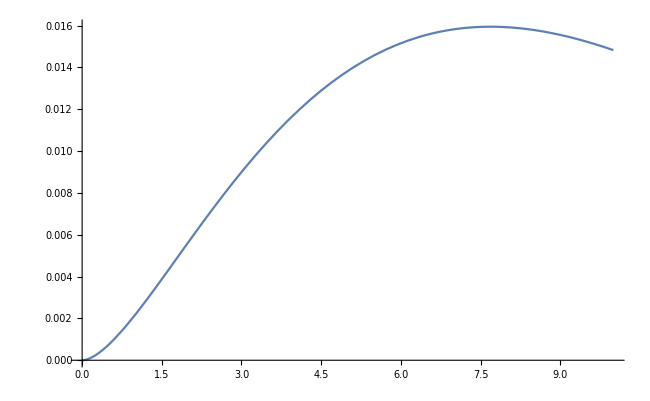

```mathematica
Plot[-4π σcont[[1]] r^2 Im[ϵ[r,15/100,155/1000]],{r,0,10},PlotRange->All]
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVsold[r_,mD_,α_,σ_,T_]:=-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

## Combined

```mathematica
ReVc[r,mD,α]
```

-mD α-(ⅇ^(-mD r) α)/r

```mathematica
ImVc[r,mD,α,T]
```

T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞}]

```mathematica
ReVs[r,mD,σ]
```

(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD

```mathematica
ImVs[r,mD,σ,T]
```

1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4]

```mathematica
ReVsold[r,mD,α,σ]
```

ReVsold[r,mD,α,σ]

```mathematica
ImVsold[r,mD,α,σ,T]
```

T α (-(√π NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[(s mD)/(((mD^2 σ)/α)^(1/4))],{s,0,∞},MaxRecursion→20,WorkingPrecision→10])/(2^(1/4) Gamma[3/4])+NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[(s mD)/(((mD^2 σ)/α)^(1/4))],{s,0,((mD^2 σ)/α)^(1/4) r},MaxRecursion→20,WorkingPrecision→10] ParabolicCylinderD[-1/2,√2 r ((mD^2 σ)/α)^(1/4)]+NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[(s mD)/(((mD^2 σ)/α)^(1/4))],{s,((mD^2 σ)/α)^(1/4) r,∞},MaxRecursion→20,WorkingPrecision→10] Re[ParabolicCylinderD[-1/2,ⅈ √2 r ((mD^2 σ)/α)^(1/4)]])

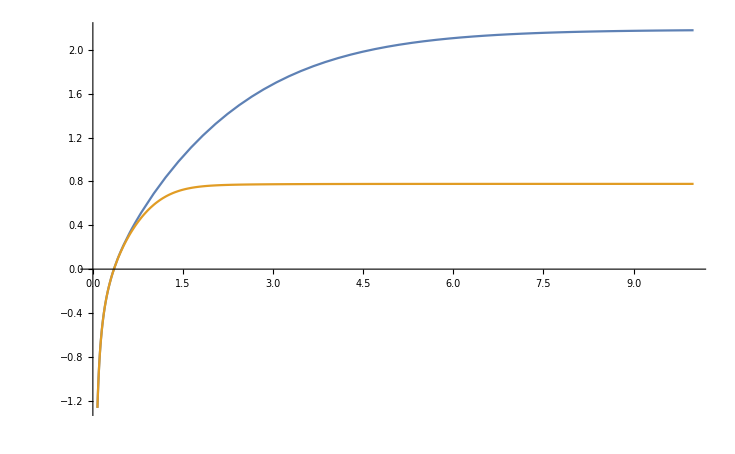

```mathematica
Block[{mD=0.15,α=αcont[[1]],σ=σcont[[1]]},Plot[{ReVc[r/0.197,mD,α]+ReVs[r/0.197,mD,σ],ReVc[r/0.197,mD,α]+ReVsold[r/0.197,mD,α,σ]},{r,0,10}]]
```

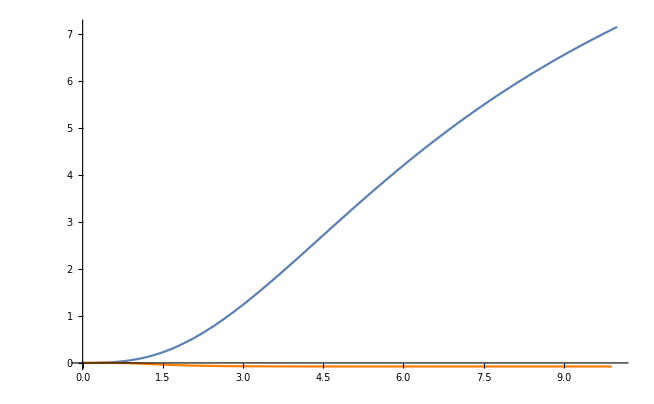

```mathematica
Block[{mD=0.15,α=αcont[[1]],σ=σcont[[1]],T=155/1000},Show[Plot[ImVc[r/0.197,mD,α,T]+ImVs[r/0.197,mD,σ,T],{r,0,10}],DiscretePlot[ImVc[r/0.197,mD,α,T]+ImVsold[r/0.197,mD,α,σ,T],{r,10^-10,10,1/10},Joined->True,Filling->None,PlotStyle->Orange]]]
```

## Discretization

```mathematica
rmax=50.;
dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
```

```mathematica
one[n_,d_]:=DiagonalMatrix[1+0 Range[n-Abs[d]],d];
stringopgauss=(one[len,-1]-2 one[len,0]+one[len,1]);
coulopgauss=1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])-2/dr(one[len,-1]+one[len,1]);
```

```mathematica
{vals,vecs}=Eigensystem[N[coulopgauss]];
```

```mathematica
U=Transpose[vecs];
```

```mathematica
eigeninter=Interpolation[Transpose[{rlist,vals}]];
```

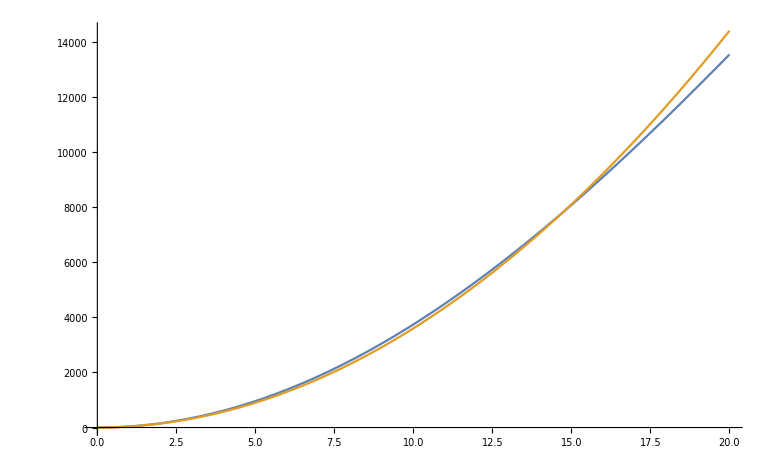

```mathematica
Plot[{eigeninter[x]-eigeninter[0.01],36 x^2},{x,0.01,20}]
```

```mathematica
eigeninter[0.01]
```

-39600.

```mathematica
deltatrans=Inverse[U].Array[KroneckerDelta,{len,len}].U;
```

```mathematica
deltatrans[[;;10,;;10]]//MatrixForm
```

(1. | -5.80876×10^-17 | 1.04238×10^-16 | 6.62434×10^-17 | -1.03226×10^-16 | 1.1082×10^-16 | 1.0156×10^-16 | -1.68226×10^-16 | 2.55607×10^-17 | -2.75792×10^-17
-1.74365×10^-17 | 1. | 3.11227×10^-16 | 2.72464×10^-17 | -2.17113×10^-16 | -1.58124×10^-17 | 1.00518×10^-16 | -1.03131×10^-16 | -6.52051×10^-17 | -5.90871×10^-17
-2.45738×10^-16 | -1.22916×10^-16 | 1. | -8.62118×10^-17 | 1.48646×10^-16 | -2.38409×10^-16 | 2.56982×10^-16 | -1.87026×10^-16 | 2.50416×10^-17 | 1.17731×10^-16
-1.32565×10^-16 | -1.79228×10^-16 | -5.0772×10^-17 | 1. | -4.48544×10^-17 | 1.4158×10^-16 | -7.16299×10^-16 | 2.5158×10^-16 | -2.23395×10^-16 | -3.20413×10^-16
1.17071×10^-17 | 2.04956×10^-17 | -1.05491×10^-16 | 7.85139×10^-17 | 1. | 4.51282×10^-16 | -9.03782×10^-17 | -2.22422×10^-17 | -1.39228×10^-16 | -2.90996×10^-16
-1.12999×10^-16 | -7.64856×10^-17 | -4.6572×10^-17 | -7.52168×10^-17 | -2.55169×10^-17 | 1. | 5.22621×10^-16 | -4.27885×10^-17 | 2.25876×10^-16 | -2.39895×10^-16
-7.10187×10^-17 | -7.04234×10^-18 | 1.22721×10^-17 | -1.16218×10^-16 | -1.4239×10^-17 | 4.56957×10^-17 | 1. | -2.89332×10^-17 | -2.00538×10^-16 | 2.60841×10^-16
1.43627×10^-17 | 4.85885×10^-17 | 8.8808×10^-17 | 2.63743×10^-17 | -6.55896×10^-17 | 8.52058×10^-17 | 1.99118×10^-17 | 1. | -2.67995×10^-16 | 1.4374×10^-16
5.89229×10^-17 | 2.67398×10^-17 | -4.31108×10^-18 | 7.16899×10^-17 | -1.40989×10^-17 | 2.10035×10^-17 | 7.08967×10^-19 | -9.07249×10^-17 | 1. | 4.09604×10^-17
-3.7226×10^-18 | 4.66585×10^-17 | -1.06025×10^-17 | -2.60081×10^-18 | -2.72582×10^-17 | 6.00673×10^-18 | -2.68298×10^-17 | 7.09352×10^-17 | -3.91871×10^-17 | 1.)

```mathematica
ϵdis=DiagonalMatrix[Table[ϵ[r],{r,dr,rmax,dr}]];
```

```mathematica
ϵdistra=Inverse[U].ϵdis.U;
```

```mathematica
ϵdistra1=U.ϵdis.Inverse[U];
```

```mathematica
ϵdistra[[;;10,;;10]]//MatrixForm
```

(-0.00146953+0.00442974 ⅈ | -0.0014631+0.00392421 ⅈ | 0.00108758-0.00219177 ⅈ | 0.000850564-0.00132663 ⅈ | -0.000688219+0.000863331 ⅈ | 0.000579548-0.000611518 ⅈ | 0.000498112-0.000449632 ⅈ | -0.000437747+0.000347716 ⅈ | 0.000389451-0.000274194 ⅈ | 0.00035131-0.000223558 ⅈ
-0.0014631+0.00392421 ⅈ | -0.00255711+0.0066215 ⅈ | 0.00231366-0.00525084 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00118633-0.00131296 ⅈ | 0.0010173-0.000959234 ⅈ | -0.000887563+0.000723826 ⅈ | 0.000789058-0.000571274 ⅈ | 0.000708921-0.000458486 ⅈ
0.00108758-0.00219177 ⅈ | 0.00231366-0.00525084 ⅈ | -0.00324533+0.00748484 ⅈ | -0.00289321+0.00586235 ⅈ | 0.00227391-0.00350473 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00157578+0.00158716 ⅈ | 0.00136861-0.00118279 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00108231+0.000726885 ⅈ
0.000850564-0.00132663 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00289321+0.00586235 ⅈ | -0.00374344+0.00793447 ⅈ | 0.00333096-0.00621007 ⅈ | -0.00266336+0.00377892 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00166186+0.0013384 ⅈ | -0.00147775+0.00104037 ⅈ
-0.000688219+0.000863331 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00227391-0.00350473 ⅈ | 0.00333096-0.00621007 ⅈ | -0.0041329+0.00820866 ⅈ | 0.00368227-0.00643363 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00216597-0.0019037 ⅈ | 0.00191347-0.00145288 ⅈ
0.000579548-0.000611518 ⅈ | 0.00118633-0.00131296 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00266336+0.00377892 ⅈ | 0.00368227-0.00643363 ⅈ | -0.00445237+0.00839295 ⅈ | -0.00397552+0.00658924 ⅈ | 0.00325355-0.00409547 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00240081+0.00200319 ⅈ
0.000498112-0.000449632 ⅈ | 0.0010173-0.000959234 ⅈ | -0.00157578+0.00158716 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00397552+0.00658924 ⅈ | -0.00472309+0.00852521 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00348839+0.00419496 ⅈ | -0.00298434+0.00286723 ⅈ
-0.000437747+0.000347716 ⅈ | -0.000887563+0.000723826 ⅈ | 0.00136861-0.00118279 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00325355-0.00409547 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00495792+0.00862469 ⅈ | 0.00444744-0.00679144 ⅈ | 0.00369573-0.00427249 ⅈ
0.000389451-0.000274194 ⅈ | 0.000789058-0.000571274 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00166186+0.0013384 ⅈ | 0.00216597-0.0019037 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00348839+0.00419496 ⅈ | 0.00444744-0.00679144 ⅈ | -0.00516526+0.00870223 ⅈ | -0.00464335+0.00686079 ⅈ
0.00035131-0.000223558 ⅈ | 0.000708921-0.000458486 ⅈ | -0.00108231+0.000726885 ⅈ | -0.00147775+0.00104037 ⅈ | 0.00191347-0.00145288 ⅈ | -0.00240081+0.00200319 ⅈ | -0.00298434+0.00286723 ⅈ | 0.00369573-0.00427249 ⅈ | -0.00464335+0.00686079 ⅈ | -0.00535085+0.00876434 ⅈ)

```mathematica
ϵdis1=ParallelTable[ϵ[r],{r,dr,rmax,dr}];
```

```mathematica
ϵdisp1=Fourier[ϵdis1];
```

```mathematica
ϵdisp=ParallelTable[ϵp[p],{p,-1,1,0.001}];
```

```mathematica
ϵdisp2=Fourier[ϵdisp]
```

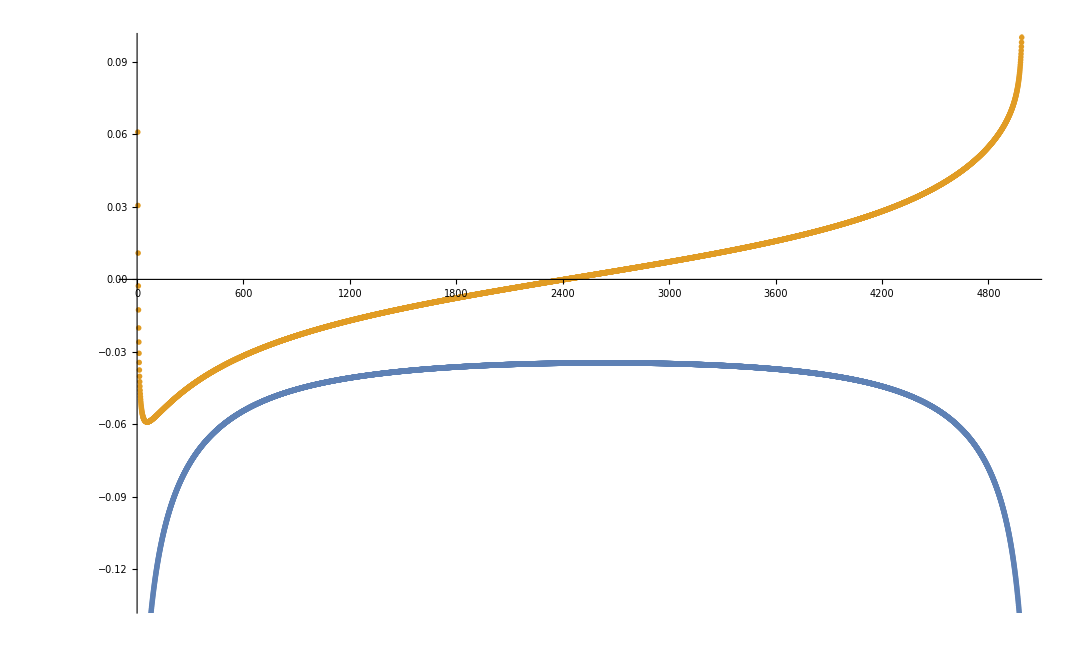

```mathematica
ListPlot[{Re[ϵdisp1],Im[ϵdisp1]}]
```

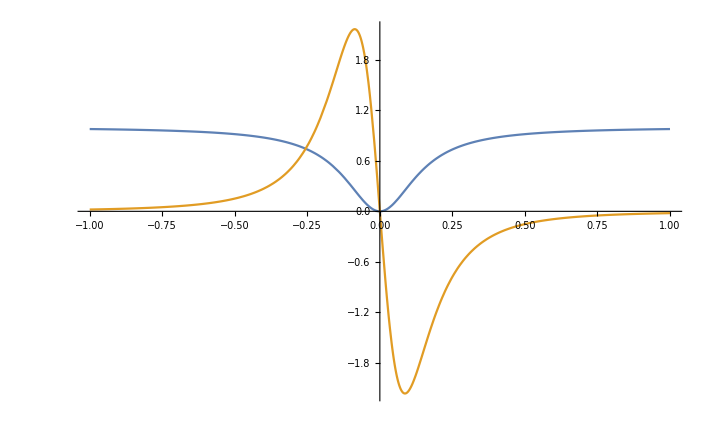

```mathematica
Plot[{p^2/(p^2+mD^2),-(p mD^2)/((p^2+mD^2)^2)},{p,-1,1}]
```